```mathematica
model="psi";
loadNotebook["inz_off_model_"<>model<>".nb"];
```

```mathematica
wyliczSterowanieFuzji[rozwiazanieu_]:=(
thetau1[t_] = (Subscript[θ, u1][t]/. rozwiazanieu)[[1]];
thetau1[t_] = Mod[thetau1[t]-Pi/2, 2Pi];
thetau2[t_] = (Subscript[θ, u2] [t]/. rozwiazanieu)[[1]];
thetau2[t_] = Mod[thetau2[t]-Pi/2, 2Pi];

psi1[t_] = (Subscript[ϕ, u1][t] /. rozwiazanieu)[[1]];
psi2[t_] = (Subscript[ϕ, u2][t] /. rozwiazanieu)[[1]];


r[t_] = .;
w = Solve[{r[t]==0.03*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )],  Tan[a[t]] ==(Sin[Subscript[θ, 1][t]])/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])}, {Subscript[ϕ, 1][t],Subscript[θ, 1][t]}];
w5 = w[[5]];
w5 = w5 /. {a[t]->Subscript[θ, u1][t]/. rozwiazanieu};
w5 = w5 /. { r[t]->0.02};(*promien1[t], 0.02*)

phi15[t_] = ((Subscript[ϕ, 1][t]  /. w5))[[1]];
theta15[t_] = (Subscript[θ, 1][t]  /. w5)[[1]];

phi1[t_] = Which[thetau1[t]< Pi - 0.001 && thetau1[t] > 0.001, -phi15[t],thetau1[t]> Pi + 0.001 && thetau1[t] < 2Pi-0.001, phi15[t], True, 0];
theta1[t_] = If[thetau1[t]< Pi, -theta15[t], theta15[t]];

w5 = w[[5]];
w5 = w5 /. {a[t]->Subscript[θ, u2][t]/. rozwiazanieu};
w5 = w5 /. { r[t]-> 0.02};

phi25[t_] = ((Subscript[ϕ, 1][t]  /. w5))[[1]];
theta25[t_] = (Subscript[θ, 1][t]  /. w5)[[1]];

phi2[t_] = Which[thetau2[t]< Pi - 0.001 && thetau2[t] > 0.001, -phi25[t],thetau2[t]> Pi + 0.001 && thetau2[t] < 2Pi-0.001, phi25[t], True, 0];
theta2[t_] = If[thetau2[t]< Pi, -theta25[t], theta25[t]];
{phi1[t],theta1[t],psi1[t],phi2[t],theta2[t],psi2[t]}
);
```

```mathematica
rozwiazRownaniaFuzji[tmax_]:=(
(*{phi1[t_],theta1[t_],psi1[t_],phi2[t_],theta2[t_],psi2[t_]}=ster;*)
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
(*WAZNE JAK W CHUJ SPASOWAC WARUNKI POCZATKOWE NJA THETA 0*)
If[model=="psi",
tosolve = (rownanie /.{Subscript[η, 1][t] ->phi1'[t], Subscript[η, 2][t]->theta1'[t],Subscript[η, 3][t]->psi1'[t],Subscript[η, 4][t]->phi2'[t],Subscript[η, 5][t]->theta2'[t], l-> 0.1, R-> 0.03}) ~Join~ {x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, Subscript[ϕ, 1][0]==phi1[0], Subscript[θ, 1][0]==theta1[0], Subscript[ψ, 1][0]==psi1[0],Subscript[ϕ, 2][0]==phi2[0], Subscript[θ, 2][0]==theta2[0], Subscript[ψ, 2][0]==psi2[0]};,

tosolve = (rownanie /.{Subscript[η, 1][t] ->phi1'[t], Subscript[η, 2][t]->theta1'[t],Subscript[η, 3][t]->psi1'[t],Subscript[η, 4][t]->theta2'[t],Subscript[η, 5][t]->psi2'[t], l-> 0.1, R-> 0.03}) ~Join~ {x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, Subscript[ϕ, 1][0]==phi1[0], Subscript[θ, 1][0]==theta1[0], Subscript[ψ, 1][0]==0,Subscript[ϕ, 2][0]==phi2[0], Subscript[θ, 2][0]==theta2[0], Subscript[ψ, 2][0]==psi2[0]};
]
rozwiazanief = NDSolve[tosolve, {x,y, Subscript[θ, 0],Subscript[ϕ, 1], Subscript[θ, 1],Subscript[ψ, 1], Subscript[ϕ, 2], Subscript[θ, 2],Subscript[ψ, 2]}, {t,0,tmax}, Method->Automatic, MaxSteps->100000];
rozwiazanief
);
```

```mathematica
wyrysujFuzja[rozwiazanie_, h_,hd_,tmax_,anim_,i_,from_]:=Module[{},
loc="C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\";
weight="Bold";
size=15;

pod={Subscript[θ, u1][t]->ArcTan[Sin[Subscript[θ, 1][t]]/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])],Subscript[θ, u2][t]->ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]};
Plot[{(h[[1]]-hd[[1]]/.pod)/.rozwiazanie,(h[[2]]-hd[[2]]/.pod)/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->All, PlotStyle->{Thick},BaseStyle->{FontWeight->weight,FontSize->size}]//Print;

plot1=Plot[{(h[[1]]-hd[[1]]/.pod)/.rozwiazanie,(h[[2]]-hd[[2]]/.pod)/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->range, PlotStyle->{Thick},BaseStyle->{FontWeight->weight,FontSize->size}];
plot1//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_1.pdf",plot1];

plot2=Plot[{Subscript[θ, 0][t]-θd[t]/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_θ_0","e_ψ_1","e_ψ_2"},{0.90,0.75}],PlotRange->{-0.5,0.5}, PlotStyle->{Thick},BaseStyle->{FontWeight->weight,FontSize->size}];
plot2//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_2.pdf",plot2];

If[model=="psi",
plot3=Plot[{phi1'[t],phi2'[t]}, {t,0,tmax}, PlotRange->{-1,1}, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_1","η_4"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot3//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_3.pdf",plot3];,

plot3=Plot[{phi1'[t]}, {t,0,tmax}, PlotRange->{-1,1}, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_1","η_4"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot3//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_3.pdf",plot3];
];

If[model=="psi",
plot4=Plot[{theta1'[t],theta2'[t]}, {t,0,tmax}, PlotRange->{-1,1}, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_2","η_5"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot4//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_4.pdf",plot4];,

plot4=Plot[{theta1'[t],theta2'[t]}, {t,0,tmax}, PlotRange->{-1,1}, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_2","η_4"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot4//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_4.pdf",plot4];
];

plot5=Plot[{Subscript[ϕ, 1][t] /.rozwiazanie,Subscript[ϕ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"},PlotLegends->Placed[{"ϕ_1","ϕ_2"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot5//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_5.pdf",plot5];

plot6=Plot[{Subscript[θ, 1][t] /.rozwiazanie,Subscript[θ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"},PlotLegends->Placed[{"θ_1","θ_2"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot6//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_6.pdf",plot6];

plot7=Plot[{Subscript[ψ, 1]'[t] /.rozwiazanie,Subscript[ψ, 2]'[t] /.rozwiazanie}, {t,0,tmax}, PlotRange->Automatic, AxesLabel->{"t","ψ̇"},PlotLegends->Placed[{"(ψ̇)_1","(ψ̇)_2"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot7//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_7.pdf",plot7];

krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];
vd[t_] = Re[Sqrt[(xd'[t])^2+(yd'[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];plot8=ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0},BaseStyle->{FontWeight->weight,FontSize->size},AxesLabel->{"x","y"}];
plot8//Print;
Export[loc<>"inz_off_"<>model<>"_fuz_"<>from<>ToString[i]<>"_8.pdf",plot8];


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
x33[t_]=(x[t]+0.2*Sin[θd[t]]/.rozwiazanie)[[1]];
y33[t_]=(y[t]-0.2*Cos[θd[t]]/.rozwiazanie)[[1]];
x44[t_]=(xd[t]+0.1(xd'[t]/vd[t])/.rozwiazanie)[[1]];
y44[t_]=(yd[t]+0.1(yd'[t]/vd[t])/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}],
Graphics[{Thickness[0.002],Black,Line[{Dynamic[{x11[t],y11[t]}],Dynamic[{x33[t],y33[t]}]}]}],
Graphics[{Thickness[0.005],Green,Line[{Dynamic[{xd[t],yd[t]}],Dynamic[{x44[t],y44[t]}]}]}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

## FUZJA

Unset::norep: Assignment on r for r[t_] not found.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

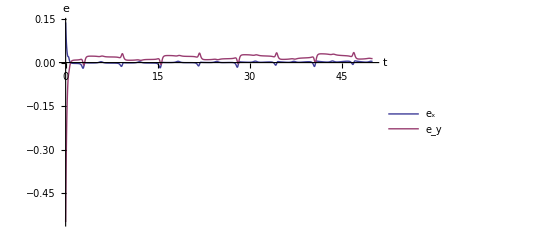

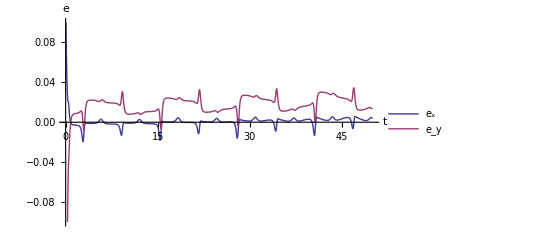

-Graphics-

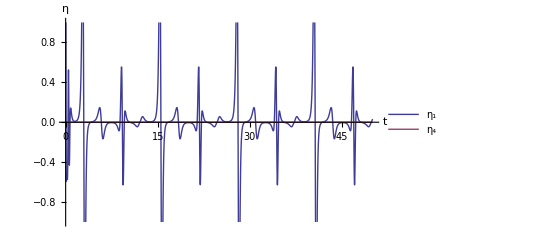

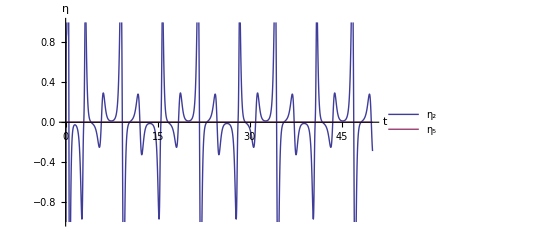

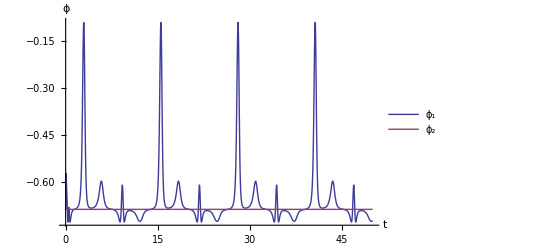

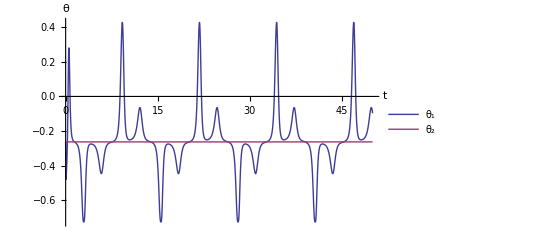

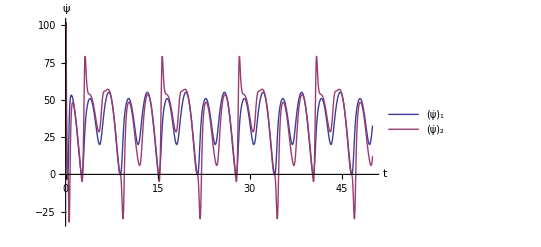

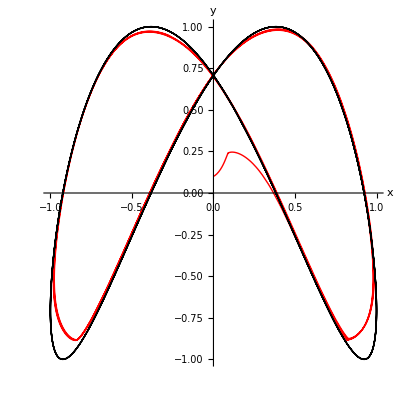

```mathematica
range={-0.1,0.1};(*If[model=="psi",{-0.1,0.1},All];*)
{phi1[t_],theta1[t_],psi1[t_],phi2[t_],theta2[t_],psi2[t_]}=wyliczSterowanieFuzji[roz];
rozwiazanief=rozwiazRownaniaFuzji[tmax];
wyrysujFuzja[rozwiazanief,h,hd,tmax,True,1, "lin_"];
```